# Versuch C1

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx}

```mathematica
temps=ToExpression[StringSplit[StringSplit[#,"="][[-1]],"."][[1]]]&/@files
```

{30,35,40,44,44}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,35.,40.1,44.1,44.6}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

## Fehler

```mathematica
σv=0.025;
σP=0.25;
```

## Plotting

{Gas, Gemischt, Flüssig}

```mathematica
colours={RGBColor[0,0.6,0], RGBColor[0.56,0.37,0.60],Blue}
```

{RGBColor[0, 0.6, 0],RGBColor[0.56, 0.37, 0.6],RGBColor[0, 0, 1]}

```mathematica
states={"Gas", "Gemischt","Flüssig"}
```

{Gas,Gemischt,Flüssig}

```mathematica
assoc=AssociationThread[states,colours];
```

```mathematica
cf[_,_]=Black;
```

```mathematica
Do[cf[data[[i,j,1]],data[[i,j,2]]]=assoc[data[[i,j,3]]],{i,1,Length[data]},{j,1,Length[data[[i]]]}]
```

{Around[#[[1]],σv],Around[#[[2]],σP]} for error bars

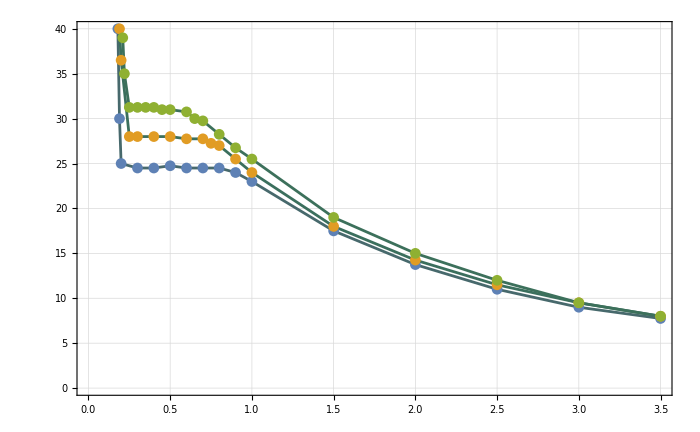

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],ColorFunction->cf,ColorFunctionScaling->False,Joined->True],ListPlot[Map[#[[1;;2]]&, data,{2}],ColorFunction->cf,ColorFunctionScaling->False],pltsettings]
```

```mathematica
ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->ColorData["ThermometerColors"]/@Rescale[temps],pltsettings,Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.02]},PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]]
```

-Graphics-

## This is the final plot

```mathematica
(*plotMarkers->{Graphics[{Disk[{0,0},Scaled[0.02]]}],Graphics[{Disk[{0,0},Scaled[0.02]]}] }*)
```

```mathematica
plotMarkers=Charting`CommonDump`GraphicsOpenPlotMarkers[][[1;;3]];
```

```mathematica
plotMarkerAssoc=AssociationThread[states,plotMarkers];
```

```mathematica
flattened=Flatten[Map[#[[1;;3]]&, data,{2}],1];
```

```mathematica
pmarkers=plotMarkerAssoc[#[[3]]]&/@flattened;
```

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

```mathematica
pcolours=Flatten[Table[ConstantArray[cols[[i]],Length[data[[i]]]],{i,1,Length[data]}],1];
```

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours]]
```

-Graphics-

## Log P Plot

```mathematica
V0=0.4
```

0.4

```mathematica
pvals=Flatten[DeleteCases[x_/;x[[1]]!=V0]/@data,1]
```

{{0.4,24.5,Gemischt},{0.4,28.,Gemischt},{0.4,31.25,Gemischt},{0.4,34.,Gemischt},{0.4,34.,Gemischt}}

```mathematica
data2=Transpose[{temps, pvals[[All,2]]}]
```

{{30.1,24.5},{35.,28.},{40.1,31.25},{44.1,34.},{44.6,34.}}

```mathematica
data2plot={1/#[[1]],Log[#[[2]]]}&/@data2;
```

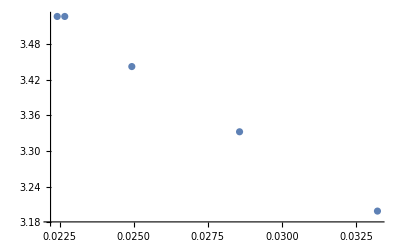

```mathematica
ListPlot[data2plot]
```